```mathematica
ClearAll["Global`*"];
W=5;U=W^2;

ShowMarking[marking_]:=Module[{},Graphics[Table[{EdgeForm[Thin],If[EvenQ[Floor[(j-1)/W]+Floor[(i-1)/W]],White,Lighter[Gray,0.5]],Rectangle[{i,j},{i+1,j+1}],Black,If[KeyExistsQ[marking,{i,j}],Text[Style[marking[{i,j}],Medium],{i+0.5,j+0.5}]]},{i,1,U},{j,1,U}]]]

ShowSolution[soln_]:=Module[{arr,r},
arr=ArrayReshape[soln,{U,U,U}];
r=Table[Flatten[Position[arr⟦i,j⟧,True]]⟦1⟧,{i,U},{j,U}];
Graphics[Table[{EdgeForm[Thin],If[EvenQ[Floor[(j-1)/W]+Floor[(i-1)/W]],White,Lighter[Gray,0.5]],Rectangle[{i,j},{i+1,j+1}],Black,Text[Style[r⟦i,j⟧,Medium],{i+0.5,j+0.5}]},{i,1,U},{j,1,U}]]]

AndList[l_]:=Fold[And,True,l];
OrList[l_]:=Fold[Or,False,l];

s=Table[Table[Table[Unique[s],{z,1,U}],{y,1,U}],{x,1,U}];

(* Sudoku rules constraints *)

f1=AndList[Table[AndList[Table[OrList[Table[s[[x,y,i]],{i,1,U}]],{x,1,U}]],{y,1,U}]];
f2=AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s[[x,y,z]]]||Not[s[[i,y,z]]],{i,x+1,U}]],{x,1,U-1}]],{z,1,U}]],{y,1,U}]];
f3=AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s[[x,y,z]]]||Not[s[[x,i,z]]],{i,y+1,U}]],{y,1,U-1}]],{z,1,U}]],{x,1,U}]];
f4=AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦W i+x,W j+y,z⟧]||Not[s⟦W i+x,W j+k,z⟧],{k,y+1,W}]],{y,1,W}]],{x,1,W}]],{j,0,W-1}]],{i,0,W-1}]],{z,1,U}]];
f5=AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦W i+x,W j+y,z⟧]||Not[s⟦W i+k,W j+l,z⟧],{l,1,W}]],{k,x+1,W}]],{y,1,W}]],{x,1,W}]],{j,0,W-1}]],{i,0,W-1}]],{z,1,U}]];
```

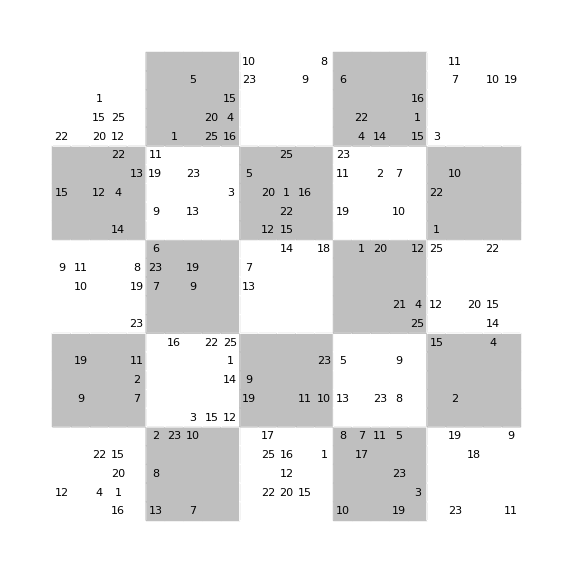

constraint set size: 563125

known problem clues: 146

$Aborted

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[soln⟦2⟧,{25,25,25}].

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of soln⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

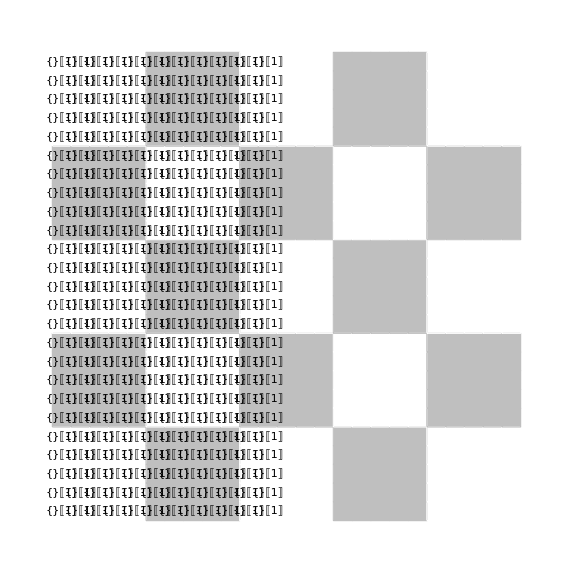

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

That took soln[[1]] seconds.

```mathematica
(* convert matrix to Association form *)
GetAssociationRules[m_?MatrixQ]:=Association@@Reap[With[{b=Dimensions[m]},
Do[If[m⟦i,j⟧≠0,Sow[{i,j}->m⟦i,j⟧]],{i,b⟦1⟧},{j,b⟦2⟧}]]]⟦2⟧;

(* mathematica can't solve? *)
mymat={
{0,12,0,0,0,0,0,0,0,0,0,0,0,9,0,0,0,15,0,0,22,0,0,0,0},{0,0,0,0,0,0,9,0,19,0,0,0,10,11,0,0,0,0,0,0,0,0,0,0,0},{0,4,0,22,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,20,15,1,0,0},{16,1,20,15,0,0,0,0,0,0,0,0,0,0,0,14,0,4,0,22,12,25,0,0,0},{0,0,0,0,0,0,7,2,11,0,23,0,19,8,0,0,0,0,13,0,0,0,0,0,0},{13,0,8,0,2,0,0,0,0,0,0,0,7,23,6,0,9,0,19,11,0,0,0,0,0},{0,0,0,0,23,0,0,0,0,16,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{7,0,0,0,10,3,0,0,0,0,0,0,9,19,0,0,13,0,23,0,0,0,0,5,0},{0,0,0,0,0,15,0,0,0,22,0,0,0,0,0,0,0,0,0,0,25,20,0,0,0},{0,0,0,0,0,12,0,14,1,25,0,0,0,0,0,0,0,3,0,0,16,4,15,0,0},{0,0,0,0,0,0,19,9,0,0,0,0,13,7,0,0,0,0,5,0,0,0,0,23,10},{0,22,0,25,17,0,0,0,0,0,0,0,0,0,0,12,0,20,0,0,0,0,0,0,0},{0,20,12,16,0,0,0,0,0,0,0,0,0,0,14,15,22,1,0,25,0,0,0,0,0},{0,15,0,0,0,0,11,0,0,0,0,0,0,0,0,0,0,16,0,0,0,0,0,9,0},{0,0,0,1,0,0,10,0,23,0,0,0,0,0,18,0,0,0,0,0,0,0,0,0,8},{10,0,0,0,8,0,13,0,5,0,0,0,0,0,0,0,19,0,11,23,0,0,0,6,0},{0,0,0,17,7,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,4,22,0,0,0},{0,0,0,0,11,0,23,0,0,0,0,0,0,0,20,0,0,0,2,0,14,0,0,0,0},{19,0,23,0,5,0,8,0,9,0,0,21,0,0,0,0,10,0,7,0,0,0,0,0,0},{0,3,0,0,0,0,0,0,0,0,25,4,0,0,12,0,0,0,0,0,15,1,16,0,0},{0,0,0,0,0,0,0,0,0,15,0,12,0,0,25,1,0,22,0,0,3,0,0,0,0},{23,0,0,0,19,0,2,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,7,11},{0,0,0,18,0,0,0,0,0,0,0,20,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,4,14,15,0,0,22,0,0,0,0,0,0,0,0,10,0},{11,0,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0}};

initial=GetAssociationRules[mymat];
fInit=AndList[Map[s⟦#⟦1⟧,#⟦2⟧,initial[#]⟧&,Keys[initial]]];
ShowMarking[initial]
Print["constraint set size: "<>ToString[Length[Flatten[f1&&f2&&f3&&f4&&f5]]]];
Print["known problem clues: "<>ToString[Length[initial]]];
soln=Timing[SatisfiabilityInstances[f1&&f2&&f3&&f4&&f5&&fInit,Flatten[s],Method->"SAT"]];
(* r=ArrayReshape[soln,{U,U,U}];
Table[Table[Flatten[Position[r[[i,j]],True]][[1]],{j,1,U}],{i,1,U}]//TableForm *)
ShowSolution[soln⟦2⟧]
Print["That took "<>ToString[soln⟦1⟧]<>" seconds."];
Beep[];
```

Need to create routines for:
	1. convert puzzle to canonical form
	2. search for minimal clue puzzles
		a. remove two, insert one until only one solution exists
	3. database search
		a. special case for puzzles with < 256 states: single line per solution
		b. more general database
	4. ?

Starting...

```mathematica
(* search from a starting position to find smaller total guess puzzles *)
Block[{workclues,cluesum,temp,atempts,aclues,i,j,k,n,x,y,r,arr},
workclues = Normal[initial];
cluesum=Length[workclues]; (* reduce this amount *)
atempts=0;
While[True,
(* try sudoku, finding two instances quicker than total count. since SatisfiabilityInstances[] cannot include multiple solutions in the general case one must get a solution and then exclude that solution with another clause *)
atempts++;
aclues=Association[workclues];
soln=SatisfiabilityInstances[f1&&f2&&f3&&f4&&f5&&AndList[Map[s⟦#⟦1⟧,#⟦2⟧,aclues[#]⟧&,Keys[aclues]]],Flatten[s]];
(* success? *)
If[Length[soln]== 1,
(* exclude that solutions and try to find another *)
arr=ArrayReshape[soln,{U,U,U}];
r=Table[Flatten[Position[arr⟦i,j⟧,True]]⟦1⟧,{i,U},{j,U}];
(* create rules for positions filled *)
arr=Reap[Do[If[Count[workclues,{i,j}->r⟦i,j⟧]==0,
Sow[s⟦i,j,r⟦i,j⟧⟧]],{i,1,U},{j,1,U}]]⟦2,1⟧;

soln=SatisfiabilityInstances[Not[AndList[arr]]&&f1&&f2&&f3&&f4&&f5&&AndList[Map[s⟦#⟦1⟧,#⟦2⟧,aclues[#]⟧&,Keys[aclues]]],Flatten[s]];

If[Length[soln]≠1,
(* only one solution *NEW*)
cluesum=Length[workclues];
Print[{Length[workclues],workclues}]];
];
(* add random rules *)
While[Length[workclues]≤cluesum,j=1;
While[j≠0,
n=RandomInteger[{1,U}];
x=RandomInteger[{1,U}];
y=RandomInteger[{1,U}];
j=Count[workclues,{x,y}->_]
+Count[workclues,{x,_}->n]
+Count[workclues,{_,y}->n]
+Count[workclues,{a_,b_}->n/;Mod[a,W]==Mod[x,W]&&Mod[b,W]==Mod[y,W]];
];AppendTo[workclues,{x,y}->n]
(*NotebookDelete[temp];
PrintTemporary[ToString[Length[workclues]]<>" atempts "<>ToString[atempts]<>", adding "<>ToString[{x,y}->n]];*)
];
(* remove clues randomly *)
While[Length[workclues]≥cluesum,
workclues=ReplacePart[workclues,RandomInteger[{1,Length[workclues]}]->Nothing]];
]];
```

```mathematica
(* high-level techniques *)

(* naked singles: intersection of two groups leaves a single digit *)

(* group missing a digit in a single sub-group,
	1. line, box/line,
	2. column, box/column,
	3. box
*)
Count[workclues,{x,y}->_]
```